# SP500 has no kurtosis

```mathematica
?FinancialData
```

```mathematica
X=Differences[Log[FinancialData["SP500",{"Nov 18 1900","Dec. 6, 2023"}]]];
```

```mathematica
Ret=Transpose[X][[2]]//Normal;
```

```mathematica
RetSq= Ret^2;
```

```mathematica
emp=EmpiricalDistribution[RetSq]
```

DataDistribution[…]

```mathematica
Kurtosis[RetSq]
```

607.33

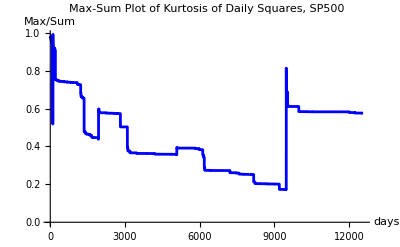

```mathematica
ListLinePlot[Table[Max[Take[RetSq^4,i]]/Total[Take[RetSq^4,i]],{i,20,Length[Ret]}],AxesLabel->{"days","Max/Sum"},PlotStyle->Blue,
PlotLabel->"Max-Sum Plot of Kurtosis of Daily Squares, SP500"]
```